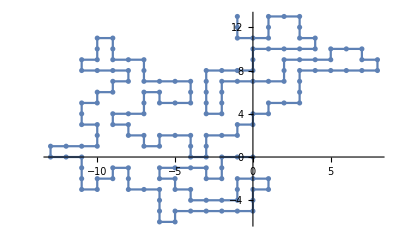

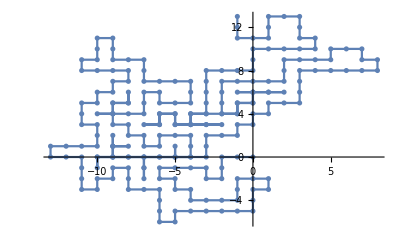

```mathematica
stack={};
visited={};
h=0;
{a1,a2}={0,0};
{a3,a4}={a1,a2};
testlist={};
AppendTo[visited,{a1,a2}];
AppendTo[stack,{a1,a2}];
AppendTo[testlist,{a1,a2}];
While[Length[visited]<200+h   ,{ Subscript[p, Length[visited]]=Show[ListPlot[stack],ListLinePlot[stack]],
{a1,a2}=RandomChoice[{{a3+1,a4},{a3-1,a4},{a3,a4+1},{a3,a4-1}}],


If[MemberQ[visited,{a1,a2}]==False,{AppendTo[visited,{a1,a2}],AppendTo[stack,{a1,a2}],{a3,a4}={a1,a2}}],

If[MemberQ[visited,{a3+1,a4}]&&MemberQ[visited,{a3-1,a4}]&&MemberQ[visited,{a3,a4+1}]&&MemberQ[visited,{a3,a4-1}]==True,{stack=Drop[stack,-1],{a3,a4}=stack[[Length[stack]]],AppendTo[visited,{a3,a4}],h=h+1}]



}]
Show[ListPlot[stack],ListLinePlot[stack]]
Show[ListPlot[visited],ListLinePlot[visited]]
```

```mathematica
gif=Table[Subscript[p, n],{n,1,Length[visited]-1}];
Export["E:\\test_gif(2).gif",gif];
SystemOpen["E:\\test_gif(2).gif"];
```